```mathematica
L=4;(*km*)
bit=25;
λ=1.55*10^-6;(*m*)
d=16;(*ps/km・nm*)
c=3*10^8;
β2=d/(2*Pi*c)λ^2*10^-3;
nm=3.96;(*電気信号の実効屈折率*)
ng=2.19;(*光波の群屈折率*)
c=3*10^8;
y=38.25*10^-3;(*mm*)
t[l_]:=l/c*(nm+ng);(*s*)
total=t[y];
initial=1000;
pitch=50*10^-6;(*um*)
pitchmm=pitch*10^3;
Δt=pitch*(nm+ng)/(3*10^8);
sumw=(total+Δt*initial)/Δt  ;
polnumber=1+IntegerPart[sumw]-initial;
electrodelength=N[pitch*polnumber];
electrodelengthmm=electrodelength*10^3;
Print[β2,"ps^2/km"]
Print[total*10^12,"ps"]
Print[Δt*10^12,"ps"]
Print[sumw,"point"]
Print["Rev pattern is", polnumber,"point"]
Print["electrodelength is",electrodelength*10^3,"mm"]
Print[electrodelengthmm,"mm"]
```

2.03931×10^-23ps^2/km

784.125ps

1.025ps

1765.point

Rev pattern is765point

electrodelength is38.25mm

38.25mm

Product Signal Wave(Cos)

一つ目の信号　1.55um

1/2 (1+Cos[400000000000000 π t])

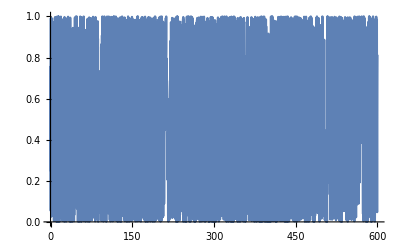

```mathematica
Fc= 200 *10^12;(*搬送波の周波数[THz]*)
carrier[t_]= (Cos[2*Pi*Fc*t]+1)/2
Plot[carrier[t], {t,0,600}]
```

位相差の式を無理やり与えて遅延を生む　→　それを30GHzに復調して図示したい

```mathematica
Phi1=(Pi*d*λ*Fc*L)/c
```

```mathematica
207.763994157405
```

```mathematica
carrier2[t_]= (Cos[2*Pi*Fc*t+207.763994157405]+1)/2
```

```mathematica
Plot[carrier2[t], {t,0,600}]
```

-Graphics-